# Cuaderno de prácticas de Matemática Discreta

## Práctica 10

## Grado en Ingeniería Informática Curso 2023/2024

## Datos personales :

Apellidos y nombre: Carrasco Vico, Juan
	DNI: 11111111 0
	Fecha de nacimiento: 25/03/2005
	Grupo de teoría: A
	Grupo de prácticas: 1

## Ejercicio 9.4.c: Aplicando el teorema de estructura de las álgebras de Boole finitas y la función BOOLE

#### Utilizando el teorema de estructuras :

```mathematica
DIAGRAMA[A_,R_]:=Module[{B,t1,nivel,R1,tabla,puntos,k1,minimales,minimal,cont,Rlocal},
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
Rlocal = R;
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},Rlocal]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
Rlocal=Complement[Rlocal,R1];
R1={};
Do[Do[If[Length[Intersection[Rlocal,{{Rlocal[[k1,1]],A[[j1]]},{A[[j1]],Rlocal[[k1,2]]}}]]==2,R1=Union[R1,{Rlocal[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[Rlocal]}];
Rlocal=Complement[Rlocal,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[Rlocal[[t1,1]]],Coord[Rlocal[[t1,2]]]}]];,{t1,1,Length[Rlocal]}];
Print["Diagrama de orden:"];
Show[Graphics[puntos],AspectRatio->1,Background->None]];
```

```mathematica
A ={5,3,1};
conD = Subsets[A]
R={};
Do[
Do[
If[Intersection[conD[[n]],conD[[m]]]== conD[[n]],
AppendTo[R,{conD[[n]],conD[[m]]}];
];
,{m,1,Length[conD]}];
,{n,1,Length[conD]}];
Print["El conjunto D es: ", conD];
Print["La relación binaria E es: ",R];
```

{{},{5},{3},{1},{5,3},{5,1},{3,1},{5,3,1}}

El conjunto D es: {{},{5},{3},{1},{5,3},{5,1},{3,1},{5,3,1}}

La relación binaria E es: {{{},{}},{{},{5}},{{},{3}},{{},{1}},{{},{5,3}},{{},{5,1}},{{},{3,1}},{{},{5,3,1}},{{5},{5}},{{5},{5,3}},{{5},{5,1}},{{5},{5,3,1}},{{3},{3}},{{3},{5,3}},{{3},{3,1}},{{3},{5,3,1}},{{1},{1}},{{1},{5,1}},{{1},{3,1}},{{1},{5,3,1}}}

Diagrama de orden:

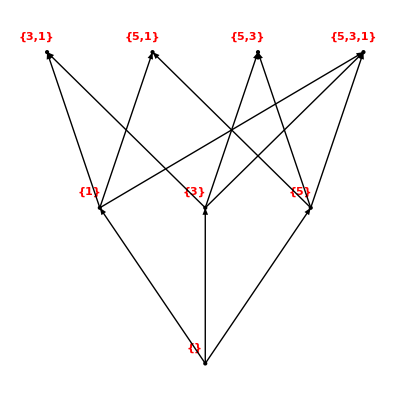

```mathematica
DIAGRAMA[conD,R]
```

Diagrama de orden:

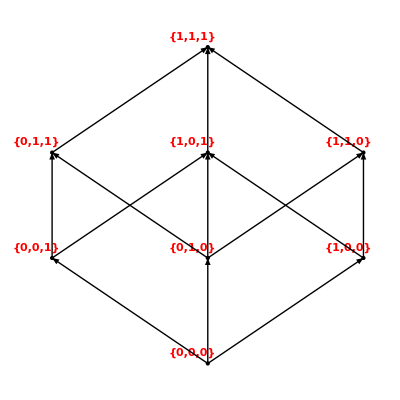

```mathematica
B3 = {{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}};
Rb3 = {};
Do[
Do[
If[Total[B3[[n]]] < Total[B3[[m]]],
AppendTo[Rb3,{B3[[n]],B3[[m]]}];
];
,{m,1,Length[conD]}];
,{n,1,Length[conD]}];
Rb3 = Complement[Rb3, {{{0,0,1},{1,1,0}},{{1,0,0},{0,1,1}}}];
DIAGRAMA[B3,Rb3]
```

Como se puede observar, D no es isomorfo al álgebra de Boole B3, luego por el teorema de estructura de las álgebras de Boole finitas D no es álgebra de Boole.

#### Utilizando la función Boole :

```mathematica
MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},
maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales
]
```

```mathematica
MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},
minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales
]
```

```mathematica
SUPREMO[A_,B_,R_]:=Module[{cotassuperiores,csuper,supremo,mini,n,m},
cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;Break[];],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
supremo={};
Do[mini=True;
Do[If[MemberQ[R,{cotassuperiores[[n]],cotassuperiores[[m]]}], ,mini=False;Break[];],{m,1,Length[cotassuperiores]}];
If[mini,AppendTo[supremo,cotassuperiores[[n]]];
Break[];];,{n,1,Length[cotassuperiores]}];
supremo
]
```

```mathematica
BOOLE[L_,R_]:=Module[{minimales,cero,preimagen,supremo,i,j,k,l,n,conjunto,imagen,f,nmin},
ABoole=True;minimales=MINIMALES[L,R];
If[Length[minimales]≠1, ABoole=False,
cero=minimales[[1]];minimales=MINIMALES[Complement[L,{cero}],R];
n=Length[minimales];f[cero]:=Table[0,{i,n}];
Do[f[minimales[[i]]]=Table[If[j≠i,0,1],{j,n}];,{i,n}];
ABoole=(Length[L]==(2^n) && Length[R]==Sum[(n!/(k!(n-k)!))*2^(n-k),{k,0,n}]);
If[ABoole,
imagen=Union[{f[cero]},Table[f[minimales[[i]]],{i,Length[minimales]}]];
preimagen=Union[{cero},minimales];
l=2;
While[l≤n && ABoole,
conjunto={};j=1;nmin=Length[minimales];
While[j≤nmin && ABoole,
i=j+1;
While[i≤nmin && ABoole,
If[Length[Position[f[minimales[[i]]]+f[minimales[[j]]],0]]==n-l,
supremo=SUPREMO[L,{minimales[[i]],minimales[[j]]},R][[1]];
If[Intersection[preimagen,{supremo}]=={},
conjunto=Union[conjunto,{supremo}];
f[supremo]=Table[If[(f[minimales[[i]]]+f[minimales[[j]]])[[k]]≠0,1,0],{k,n}];
imagen=Union[imagen,{f[supremo]}];
preimagen=Union[preimagen,{supremo}];
,If[Intersection[{supremo},conjunto]=={},ABoole=False;];
];];i++;];j++;];
minimales=conjunto;
ABoole=(Length[conjunto]==(n!/(l!*(n-l)!)));
l++;];
ABoole=(Length[imagen]==2^n && Length[preimagen]==2^n);
];];
If[ABoole,
Print["Es álgebra de Boole, un isomorfismo con ", Superscript["𝔹_2",n]," viene dado por:"];
Do[Print[L[[i]]," → ",f[L[[i]]]];,{i,2^n}];
,
Print["No es álgebra de Boole"];];
];
```

```mathematica
BOOLE[conD,R]
```

No es álgebra de Boole

## Ejercicio 9.5.c: Aplicando el teorema de estructura de las álgebras de Boole finitas y la función BOOLE

#### Utilizando el teorema de estructuras :

```mathematica
producto = 5 3 1;
conD=Divisors[producto];
R={};
Do[
Do[
If[Mod[conD[[m]],conD[[n]]]==0,
AppendTo[R,{conD[[n]],conD[[m]]}];
];
,{m,1,Length[conD]}];
,{n,1,Length[conD]}];
Print["El conjunto D es: ", conD];
Print["La relación binaria E es: ",R];
```

El conjunto D es: {1,3,5,15}

La relación binaria E es: {{1,1},{1,3},{1,5},{1,15},{3,3},{3,15},{5,5},{5,15},{15,15}}

Diagrama de orden:

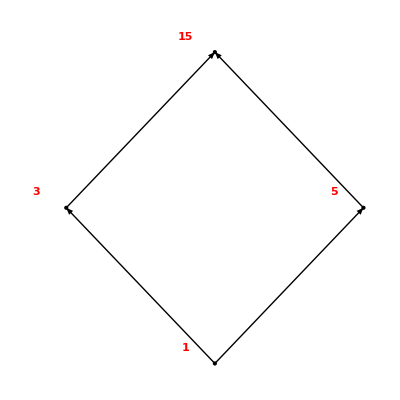

```mathematica
DIAGRAMA[conD,R]
```

Diagrama de orden:

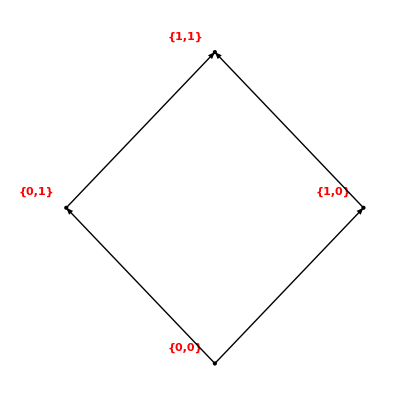

```mathematica
B2 = {{0,0},{0,1},{1,0},{1,1}};
Rb = {{{0,0},{0,0}},{{0,0},{0,1}},{{0,0},{1,0}},{{0,0},{1,1}},
       {{0,1},{0,1}},{{0,1},{1,1}},
       {{1,0},{1,0}},{{1,0},{1,1}},
       {{1,1},{1,1}}};
DIAGRAMA[B2,Rb]
```

Como se puede observar, D es isomorfo al álgebra de Boole B2, luego por el teorema de estructura de las álgebras de Boole finitas, D es álgebra de Boole

#### Utilizando la función Boole :

```mathematica
BOOLE[conD,R]
```

Es álgebra de Boole, un isomorfismo con 𝔹_2^2 viene dado por:

1 → {0,0}

3 → {1,0}

5 → {0,1}

15 → {1,1}